# Supervised Learning

## Lectures on Machine Learning

## Introduction

## About the Presented Work

These notebooks are an interactive exploration of machine learning concepts, primarily drawn from Stanford’s CS229 course (2022), available online on platforms like YouTube. They include interactive, written functions and methods taught in the course, aiming to enhance understanding through hands-on engagement. Writing and implementing the material as Mathematica notebooks facilitates better comprehension and retention. 

In addition to these notebooks, a supplementary library in C/C++ and Kotlin is provided, offering real-world implementations of the concepts covered. These documents serve as a living reference to the lectures by Andrew Ng and the updated notes by Tengyu Ma, based on the publicly available materials. All credit for the original content belongs to the instructors and the Stanford CS229 course.

## Overview

### Definition of Supervised Learning

Suppose we have a dataset giving the living areas and prices of  houses from Portland, Oregon:

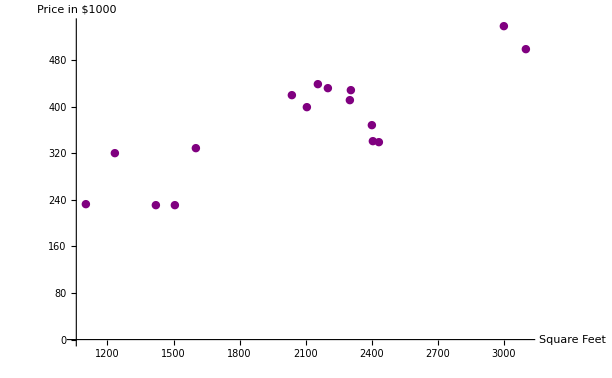

```mathematica
dataSet = {
{2104,400},{1600,330},{2400,369},{1416,232},{3000,540},{2430,340},{2153,440},{2200,432},{1502,231},{3100,500},{2300,412},{1100,234},{1230,321},{2034,420},{2304,430},{2404,341}
};
ListPlot[dataSet,PlotStyle->Purple,PlotMarkers->{"●",Thickness[Tiny]},AxesLabel->{"Square Feet","Price in $1000"},PlotRange->All]
```

How can we learn to predict the price of other houses that are note mentioned as a function of their sizes? To establish notation for future use, we’ll use  to denote the input variables, also called input features, and  to denote the output or target variable that we arey trying to predict. Each pair that we have in dataSet is called a training example. The set of all training examples is the training set. 

We would also denote the space of input values (space of acceptable inputs) and space of output values (space of acceptable outputs) as , and  respectively.

#### Formal Definition of Supervised Learning

Given a training set, learn a function  so that  is a good predictor for the corresponding value of .

For historical reasons this function is called the hypothesis. The process is therefore like below:

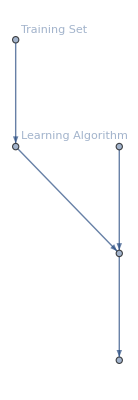

```mathematica
Graph[{
Labeled[1,"Training Set"],
Labeled[2, "Learning Algorithm"],
Labeled[3,""],
Labeled[4,""],
Labeled[5,""]
}, {1->2, 2->3, 4->3, 3->5}]
```

When the target variable that we’re trying to predict is continuous, such as our housing example, we call the learning problem a regression problem. When  can take only a small number of discrete values, we call it a classification problem.